```mathematica
hexToRGB=(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&
```

IntegerDigits[ToExpression[StringReplace[#1,#→16^^]],256,3]/255.&

```mathematica
hexToRGB["#666666"]
```

{0.4,0.4,0.4}

```mathematica
(******)
```

```mathematica
(*Header*)
```

```mathematica
speckle=Abs[Fourier[RandomComplex[{-1-ⅈ,1+ⅈ},{1000,1000}]*GaussianMatrix[{500,50}][[1;;-2,1;;-2]] ] ]^2;
speckle=Chop[speckle/Max[speckle]];
tmp=speckle[[1;;200]];
tmp2=1-Table[TukeyWindow[(i-500)/1000,0.02]*TukeyWindow[(j-500)/1000,0.01],{j,200},{i,1000}];(*Table[(If[i<=10,ⅇ^(-i/10),0]+If[i>=1000-10,ⅇ^((i-1000)/10),0])*(If[j<=10,ⅇ^(-j/10),0]),{j,200},{i,1000}];*)
tmp3=Show[
ArrayPlot[tmp, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[#,0,0]&), ColorFunctionScaling->False],
ArrayPlot[tmp2, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0.4,0.4,0.4,#]&), ColorFunctionScaling->False]
,ImageSize->{1000,200}, Frame->False]
```

-Graphics-

```mathematica
Export["/home/jb601/Documents/SitoInternet/2023/images/header.jpg", tmp3,ImageSize->{1000,200}, ImagePadding->None, PlotRangePadding->None, Background->RGBColor[0.4,0.4,0.4] ]
```

/home/jb601/Documents/SitoInternet/2023/images/header.jpg

```mathematica
TukeyWindow
```

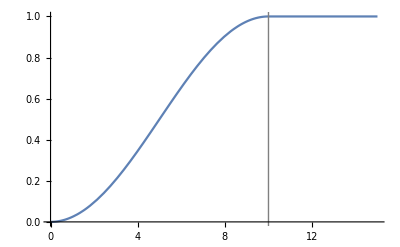

```mathematica
Plot[TukeyWindow[(x-500)/1000,0.02],{x,0,15}, PlotRange->All, Epilog->{Gray, Line[{{10,-5},{10,5}}]}]
```

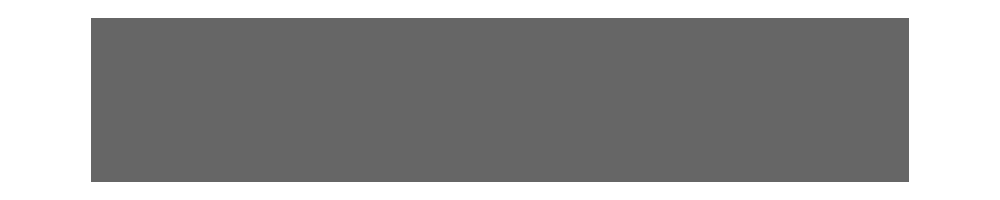

```mathematica
(*Menu*)
menum=Table[1,{j,40},{i,1000}];
shadingm=1-Table[TukeyWindow[(i-500)/1000,0.02],{j,40},{i,1000}];
menu=Show[
ArrayPlot[menum, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0,0,0]&), ColorFunctionScaling->False],
ArrayPlot[shadingm, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0.4,0.4,0.4,#]&), ColorFunctionScaling->False]
,ImageSize->1000, ImagePadding->None, PlotRangePadding->None]
```

```mathematica
Export["/home/jb601/Documents/SitoInternet/2023/images/menu.jpg", menu,ImageSize->{1000,40}, ImagePadding->None, PlotRangePadding->None, Background->None, Antialiasing->False
]
```

/home/jb601/Documents/SitoInternet/2023/images/menu.jpg

```mathematica
tmp=ArrayPlot[0.4*shadingm, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[#,#,#]&), ColorFunctionScaling->False, Background->Black]
```

-Graphics-

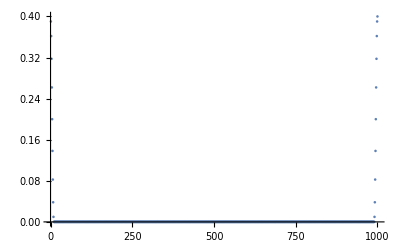

```mathematica
ListPlot[0.4shadingm[[1]]]
```

```mathematica
(*content*)
```

```mathematica
contentm=Table[1,{j,10},{i,1000}];
shadingm=1-Table[TukeyWindow[(i-500)/1000,0.02],{j,10},{i,1000}];
content=Show[
ArrayPlot[contentm, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[188/256,188/256,188/256,#]&), ColorFunctionScaling->False],
ArrayPlot[shadingm, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0.4,0.4,0.4,#]&), ColorFunctionScaling->False]
, Frame->False, ImagePadding->None, PlotRangePadding->None]
```

-Graphics-

```mathematica
Export["/home/jb601/Documents/SitoInternet/2023/images/content.jpg", content,ImageSize->{1000,10}, ImagePadding->None, PlotRangePadding->None]
```

/home/jb601/Documents/SitoInternet/2023/images/content.jpg

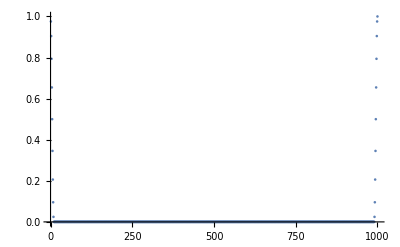

```mathematica
ListPlot[shadingm]
```

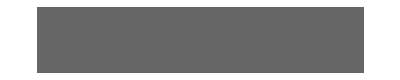

```mathematica
ArrayPlot[shadingm[[All,1;;20]], ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0.4,0.4,0.4,#]&), ColorFunctionScaling->False]
```

```mathematica
188/256//N
```

0.734375

```mathematica
Show[
ArrayPlot[contentm[[All,1;;1000]], ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[188/256,188/256,188/256,#]&), ColorFunctionScaling->False],
ArrayPlot[shadingm[[All,1;;1000]], ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0.4,0.4,0.4,#]&), ColorFunctionScaling->False]
]
```

-Graphics-

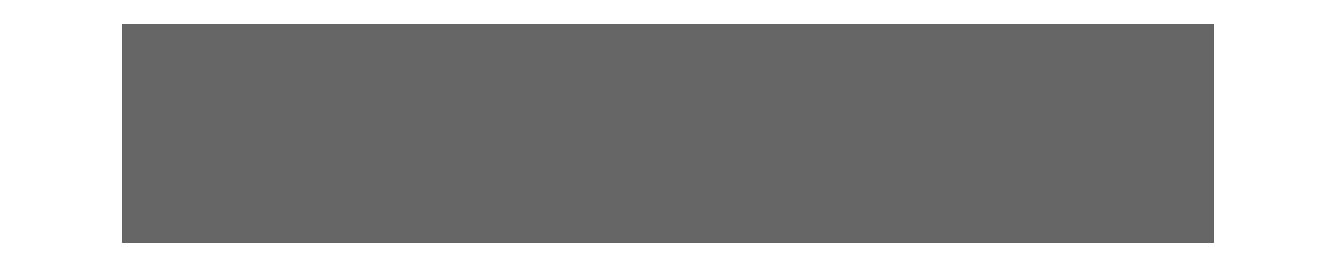

```mathematica
(*bottom*)
```

```mathematica
bottomm=Table[1,{j,20},{i,1000}];
shadingm=1-Table[TukeyWindow[(i-500)/1000,0.02]*TukeyWindow[(j-5)/20,0.5],{j,20},{i,1000}];
bottom=Show[
ArrayPlot[bottomm, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[188/256,188/256,188/256,#]&), ColorFunctionScaling->False],
ArrayPlot[shadingm, ImagePadding->None, PlotRangePadding->None,ColorFunction->(RGBColor[0.4,0.4,0.4,#]&), ColorFunctionScaling->False]
,ImageSize->1000, ImagePadding->None, PlotRangePadding->None]
```

-Graphics-

```mathematica
Export["/home/jb601/Documents/SitoInternet/2023/images/bottom.jpg",bottom,ImageSize->{1000,20}, ImagePadding->None, PlotRangePadding->None]
```

/home/jb601/Documents/SitoInternet/2023/images/bottom.jpg